## Packages and definitions

```mathematica
SetDirectory[NotebookDirectory[]];Get["/Users/gabrielaperez/Desktop/Cosas de Prácticas/libs/QuantumWalks.wl"]
```

```mathematica
SetDirectory[NotebookDirectory[]];Get["/Users/gabrielaperez/Desktop/Cosas de Prácticas/libs/QMB.wl"]
```

```mathematica
CircleEq[α_,ϕ_,β_,γ_,θ_,φ_]:=Cos[α]*Cos[θ]+Sin[α]*Sin[θ]*Cos[ϕ-φ]-(Cos[α]*Cos[β]+Sin[α]*Sin[β]*Cos[ϕ-γ])
```

```mathematica
Azimuthal[ϕ_]:=Mod[ϕ+Pi,2 Pi]-Pi
```

## 1.

```mathematica
SeedRandom[30946];
α=RandomReal[{0,Pi}]
β=Pi/2.;(*Estado inicial sobre el plano XY*)
{ϕ,γ}=RandomReal[{0,2*Pi},2]
```

0.339443

{4.12666,2.05662}

```mathematica
CircleEq[α,ϕ,β,γ,θ,φ]==0
```

0.677503+0.2782 Cos[4.12666-φ]==0

```mathematica
θ=Pi/2.;(*intersección con el plano xy*)
φsols=φ/.#&/@Solve[CircleEq[α,ϕ,β,γ,θ,φ]==0,φ]
ClearAll[θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{2.05662,6.1967}

```mathematica
(*vectores en coordenadas cartesianas de las soluciones*)
vecs=Chop@FromSphericalCoordinates[{1,Pi/2.,Azimuthal[#]}]&/@φsols
```

{{-0.466936,0.884291,0},{0.996263,-0.0863745,0}}

```mathematica
Module[{n,circxy,sphere,blochVectorψ0},
n=FromSphericalCoordinates[{1.,α,Azimuthal[ϕ]}];(*eje de rotación*)
blochVectorψ0=Chop@FromSphericalCoordinates[{1,β,Azimuthal[γ]}];
circ2=Table[RotationMatrix[θ,n].blochVectorψ0,{θ,0,2 Pi,Pi/20}];(*rotation matrix*)
circxy=Table[{Cos[θ],Sin[θ],0},{θ,0,2 Pi,Pi/20}];(*Intersección con plano xy*)
sphere=Graphics3D[{Opacity[0.2],Sphere[{0,0,0},1]}];(*Esfera unitaria*)

Graphics3D[
{
sphere[[1]],(*Esfera*)
Red,Arrow[{{0,0,0},n}],(*rotation axis*)
Black,Style[Text["",n+0.05],FontSize->20],
{Magenta,Dashed,Arrow[{{0,0,0},vecs[[1]].n*n}]},
{Magenta,Dashed,Arrow[{{0,0,0},vecs[[1]]-vecs[[1]].n*n}]},
Magenta,Arrow[{{0,0,0},vecs[[1]]}],(*initial coin state*)
Black,Style[Text["",vecs[[1]]+{0,0,0.1}],FontSize->20],
{Black,Dashed,Arrow[{{0,0,0},vecs[[2]].n*n}]},
{Black,Dashed,Arrow[{{0,0,0},vecs[[2]]-vecs[[2]].n*n}]},
Black,Arrow[{{0,0,0},vecs[[2]]}],(*initial coin state*)
Black,Style[Text["",vecs[[2]]+{0.1,0.1,0}],FontSize->20],
Black,Style[Text["",vecs[[2]]-vecs[[2]].n*n-0.1],FontSize->20],
Black,Style[Text["",vecs[[1]]-vecs[[1]].n*n+0.1],FontSize->20],
(*Black,Arrow[{{0,0,0},RotationMatrix[4.084,n].blochVectorψ0}],*)
Blue,Line[circxy],  (*Círculo en azul*)
Orange,Line[circ2]
},
Boxed->True,
Axes->True,
AxesLabel->{"x","y","z"},
LabelStyle->Directive[Black,FontSize->15],
PlotRange->ConstantArray[{-1,1},3],
ImageSize->500
]
]
```

Syntax::bktmop: Expression "*)" has no opening "(".

```mathematica
n=FromSphericalCoordinates[{1,α,Azimuthal[ϕ]}];(*eje de rotacion*)

(*Proyección de v1 y v2 al plano que define la rotación*)
v1proj=Normalize[vecs[[1]]-vecs[[1]].n*n];
v2proj=Normalize[vecs[[2]]-vecs[[2]].n*n];

θ=ArcCos[v1proj.v2proj]
```

2.19169

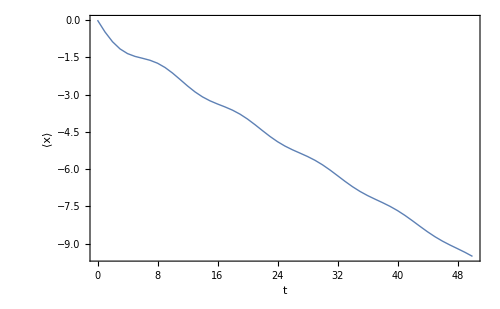

```mathematica
ψ0=Qubit[β,γ];t=1;
c=MatrixExp[-I*θ/2*(n.(Pauli/@{1,2,3}))];

ListPlot[Table[{t,Chop@ExpValPosition[DTQW[ψ0,t,c],t]},{t,0,50}],
Joined->True,
PlotStyle->Thick,
Frame->True,
FrameStyle->Directive[Black,FontSize->24],
FrameLabel->{TraditionalForm@HoldForm@t,"⟨x⟩"},
ImageSize->500
]
```

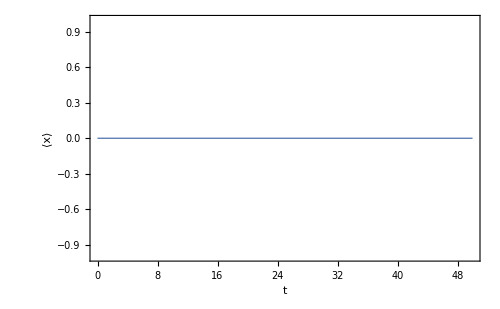

```mathematica
ψ0=Qubit[β,γ];t=1;
c=MatrixExp[-I*(2Pi-θ)/2*(n.(Pauli/@{1,2,3}))];

ListPlot[Table[{t,Chop@ExpValPosition[DTQW[ψ0,t,c],t]},{t,0,50}],
Joined->True,
PlotStyle->Thick,
Frame->True,
FrameStyle->Directive[Black,FontSize->24],
FrameLabel->{TraditionalForm@HoldForm@t,"⟨x⟩"},
ImageSize->500
]
```

## 2do Ejemplo

```mathematica
SeedRandom[30945];
α=RandomReal[{0,Pi}]
β=Pi/2.;(*Estado inicial sobre el plano XY*)
{ϕ,γ}=RandomReal[{0,2*Pi},2]
```

2.17307

{5.86059,3.01548}

```mathematica
CircleEq[α,ϕ,β,γ,θ,φ]==0
```

1.11768+0.670247 Cos[5.86059-φ]==0

```mathematica
θ=Pi/2.;
φsols=φ/.#&/@Solve[CircleEq[α,ϕ,β,γ,θ,φ]==0,φ]
ClearAll[θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{3.01548,8.70569}

```mathematica
vecs=Chop@FromSphericalCoordinates[{1,Pi/2.,Azimuthal[#]}]&/@φsols
```

{{-0.992059,0.125777,0},{-0.752409,0.658696,0}}

```mathematica
Module[{n,circ2,circxy,sphere,blochVectorψ0},
n=FromSphericalCoordinates[{1.,α,Azimuthal[ϕ]}];(*eje de rotación*)
blochVectorψ0=Chop@FromSphericalCoordinates[{1,β,Azimuthal[γ]}];
circ2=Table[RotationMatrix[θ,n].blochVectorψ0,{θ,0,2 Pi,Pi/20}];(*rotation matrix*)
circxy=Table[{Cos[θ],Sin[θ],0},{θ,0,2 Pi,Pi/20}];(*Intersección con plano xy*)
sphere=Graphics3D[{Opacity[0.2],Sphere[{0,0,0},1]}];(*Esfera unitaria*)

Graphics3D[
{
sphere[[1]],(*Esfera*)
Red,Arrow[{{0,0,0},n}],(*rotation axis*)
Black,Style[Text["",n+0.05],FontSize->20],
{Magenta,Dashed,Arrow[{{0,0,0},vecs[[1]].n*n}]},
{Magenta,Dashed,Arrow[{{0,0,0},vecs[[1]]-vecs[[1]].n*n}]},
Magenta,Arrow[{{0,0,0},vecs[[1]]}],(*initial coin state*)
Black,Style[Text["",vecs[[1]]+{0,0,0.1}],FontSize->20],
{Black,Dashed,Arrow[{{0,0,0},vecs[[2]].n*n}]},
{Black,Dashed,Arrow[{{0,0,0},vecs[[2]]-vecs[[2]].n*n}]},
Black,Arrow[{{0,0,0},vecs[[2]]}],(*initial coin state*)
Black,Style[Text["",vecs[[2]]+{0.1,0.1,0}],FontSize->20],
Black,Style[Text["",vecs[[2]]-vecs[[2]].n*n+0.1],FontSize->20],
Black,Style[Text["",vecs[[1]]-vecs[[1]].n*n-0.07],FontSize->20],
Black,Arrow[{{0,0,0},RotationMatrix[4.084,n].blochVectorψ0}],
Blue,Line[circxy],  (*Círculo en azul*)
Orange,Line[circ2]
},
Boxed->True,
Axes->True,
AxesLabel->{"x","y","z"},
LabelStyle->Directive[Black,FontSize->15],
PlotRange->ConstantArray[{-1,1},3],
ImageSize->500
]
]
```

-Graphics3D-

```mathematica
n=FromSphericalCoordinates[{1,α,Azimuthal[ϕ]}];(*eje de rotacion*)

(*Proyección de v1 y v2 al plano que define la rotación*)
v1proj=Normalize[vecs[[1]]-vecs[[1]].n*n];
v2proj=Normalize[vecs[[2]]-vecs[[2]].n*n];

θ=ArcCos[v1proj.v2proj]
```

0.989097

```mathematica
ψ0=Qubit[β,γ];t=1;
c=MatrixExp[-I*θ/2*(n.(Pauli/@{1,2,3}))];

ListPlot[Table[{t,Chop@ExpValPosition[DTQW[ψ0,t,c],t]},{t,0,50}],
Joined->True,
PlotStyle->Thick,
Frame->True,
FrameStyle->Directive[Black,FontSize->24],
FrameLabel->{TraditionalForm@HoldForm@t,"⟨x⟩"},
ImageSize->500
]
```

-Graphics-